```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S7_surfaces/surfacediffuse

```mathematica
timestep=10
diffconst=6
radius=50
binwidth=0.5
```

10

6

50

0.5

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Define functions *)
```

```mathematica
gauss[x_,mu_,sigma_]:=1/(sigma*Sqrt[2*Pi])*Exp[-(x-mu)^2/(2*sigma^2)]
```

```mathematica
Assuming[s>0,Integrate[gauss[x,mu,s],{x,-Infinity,Infinity}]]
```

1

```mathematica
scalefactor[sigma_]:=Integrate[2*Pi*r*gauss[r,0,sigma],{r,0,Infinity}]
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["simple3aout.txt"];
```

```mathematica
simdata2=StringReplace[simdata," "->","];
```

```mathematica
simdata3=ImportString[simdata2,"CSV"];
```

```mathematica
simdata4=Drop[simdata3[[1]],1]
```

{1066,3149,5077,7202,9202,11175,13189,14910,16427,17700,19377,20885,22048,23363,24098,24736,25884,26431,27162,27595,27377,27468,27880,27620,27471,27108,26611,25972,25228,24871,23908,23239,22419,21843,20840,19790,19066,18250,17110,16319,15348,14510,13668,12486,11859,11041,10260,9323,8690,8025,7362,6842,6240,5543,5203,4659,4209,3741,3501,3065,2764,2462,2258,2015,1780,1459,1315,1272,1015,946,800,758,642,525,496,440,365,280,305,235,198,166,138,141,88,70,74,68,47,35,38,27,33,22,16,16,8,8,7,4}

```mathematica
Length[simdata4]
```

100

```mathematica
nmolec=Total[simdata4]
```

999977

```mathematica
rvector=Table[i,{i,binwidth/2,radius-binwidth/2,binwidth}];
```

```mathematica
simdata5=Transpose[{rvector,simdata4}];
```

```mathematica
sigma=Sqrt[2*diffconst*timestep]
```

2 √30

```mathematica
scalefact=scalefactor[sigma]
```

4 √(15 π)

```mathematica
theoryfn[r_]:=nmolec*Pi*((r+binwidth/2)^2-(r-binwidth/2)^2)*gauss[r,0,sigma]/scalefact
```

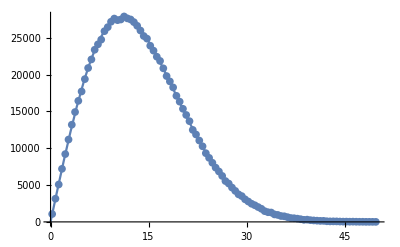

```mathematica
Show[{ListPlot[simdata5],Plot[theoryfn[x],{x,0,radius},PlotRange->All]},PlotRange->All]
```

```mathematica
residuals=Table[simdata4[[i]]-theoryfn[xvector[[i]]],{i,1,Length[simdata4]}];
```

```mathematica
residuals2=Transpose[{rvector,residuals}];
```

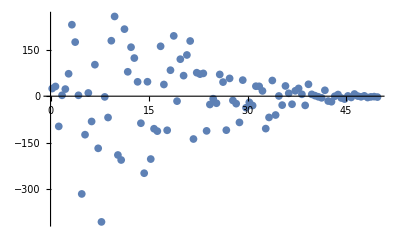

```mathematica
ListPlot[residuals2]
```